```mathematica
(* Valor de las constantes, con γy fijo *)

J=100;
(* Ecuaciones de λ y γ *)
Clear[γx,γy];
(*λ=ϵ(γx-γy)/(2(2J+1));
γ=ϵ (γx+γy)/(2(2J+1));*)
(* Valores de operadores *)
Sz[m_]=m;
SM2[m_]=Sqrt[J(J+1)-m(m+1)]*Sqrt[J(J+1)-(m+1)(m+2)];
Sm2[m_]=Sqrt[J(J+1)-m(m-1)]*Sqrt[J(J+1)-(m-1)(m-2)];
SMSm[m_]=J(J+1)-m(m-1);
SmSM[m_]=J(J+1)-m(m+1);
(* Construyendo Matrices *)
(*Paridad Positiva*)
SzMPP=Table[Sz[m]KroneckerDelta[mj,m],{mj,-J,J,2},{m,-J,J,2}];
SLMPP=Table[(SM2[m]KroneckerDelta[mj,m+2]+Sm2[m]KroneckerDelta[mj,m-2]),{mj,-J,J,2},{m,-J,J,2}];
SGMPP=Table[(SMSm[m]+SmSM[m])KroneckerDelta[mj,m],{mj,-J,J,2},{m,-J,J,2}];
(*Paridad Negativa*)
SzMPN=Table[Sz[m]KroneckerDelta[mj,m],{mj,-J+1,J,2},{m,-J+1,J,2}];
SLMPN=Table[(SM2[m]KroneckerDelta[mj,m+2]+Sm2[m]KroneckerDelta[mj,m-2]),{mj,-J+1,J,2},{m,-J+1,J,2}];SGMPN=Table[(SMSm[m]+SmSM[m])KroneckerDelta[mj,m],{mj,-J+1,J,2},{m,-J+1,J,2}];
```

```mathematica
G=1/2
Gn=0.5
```

1/2

0.5

```mathematica
Precision[G]
```

MachinePrecision

```mathematica
Precision[0.5]
```

MachinePrecision

```mathematica
N[1/2,40]
```

0.5

```mathematica
N[1/2,20]
```

0.5

```mathematica
N[Pi,40]
```

3.141592653589793238462643383279502884197

```mathematica
3.141592653589793
```

```mathematica
0.6
```

```mathematica
0.5
```

```mathematica
γxac=-(2J-1)/((2J-172)Sqrt[3])
```

-199/(28 √3)

```mathematica
N[γxac]
```

```mathematica
-4.103310841740555
```

```mathematica
N[γxac,40]-N[γxac,20]
```

```mathematica
N[98/67]
```

1.46269

```mathematica
specP1={};
vecPP={};
specN1={};
Monitor[Do[
ϵ=1;
γx=ff*γxac;
γy=3γx;

λ=ϵ(γx-γy)/(2(2J-1));
γ=ϵ (γx+γy)/(2(2J-1));
H1=ϵ SzMPP+(λ/2)SLMPP+(γ/2)SGMPP;
H2=ϵ SzMPN+(λ/2)SLMPN+(γ/2)SGMPN;
(* eigenvalores divididos en dos matrices*)
enPNO=Eigenvalues[N[H1,40]];
vecP=Eigenvectors[N[H1,40]][[Ordering[enPNO]]];
AppendTo[vecPP,vecP];
AppendTo[specP1,Sort[enPNO]];
(*enNNO=Eigenvalues[H2,40];
AppendTo[specN1,Sort[enNNO,40]];*),{ff, {1}}],N[ff]]
```

```mathematica
specP1
```

{{-623.783,-613.768,-603.857,-594.05,-584.347,-574.749,-565.255,-555.865,-546.581,-537.401,-528.326,-519.356,-510.492,-501.733,-493.079,-484.531,-476.09,-467.754,-459.525,-451.402,-443.386,-435.477,-427.676,-419.982,-412.397,-404.919,-397.55,-390.29,-383.14,-376.099,-369.169,-362.35,-355.642,-349.045,-342.562,-336.191,-329.935,-323.793,-317.767,-311.857,-306.065,-300.393,-294.84,-289.409,-284.101,-278.919,-273.864,-268.938,-264.145,-259.488,-254.97,-250.596,-246.372,-242.305,-238.403,-234.678,-231.15,-227.819,-224.868,-221.772,-220.354,-215.984,-215.83,-209.592,-209.586,-202.434,-202.434,-194.63,-194.63,-186.268,-186.268,-177.402,-177.402,-168.071,-168.071,-158.301,-158.301,-148.114,-148.114,-137.525,-137.525,-126.549,-126.549,-115.196,-115.196,-103.476,-103.476,-91.3944,-78.9594,-66.1763,-53.0499,-39.5844,-25.7836,-11.6509,2.81095,17.5992,32.7116,48.146,63.9005,79.9734,96.3631}}

```mathematica
specP1[[1,3;;-1;;2]]-specP1[[1,2;;-2;;2]]
```

{9.91114305814690109350535067,9.70276618131467030175268353,9.49396328953924475834707373,9.28469003677458535264845003,9.07489622023331570709464974,8.86452480714693726052255498,8.65351075907645225492188307,8.44177960153653231571851326,8.22924567022169068329651919,8.01580994240365282641960706,7.80135733030271279518113707,7.58575326814675965726910384,7.36883935957117121875975254,7.15042775642216718453176826,6.93029379674292884736427873,6.70816621011869508875028101,6.48371385348227586663400433,6.25652738274340814531664213,6.02609333468441409910338223,5.79175648107452514141692057,5.55266340035443823126869252,5.30767465931406917732377816,5.05522175062705256971941416,4.79306034839380096237372476,4.51781222407263935781150876,4.22402505352196031444093012,3.90188349765433981829525365,3.52749465875662080689974043,2.95053977964846645825502717,1.41802692082182621760812116,0.15391433333471787031943412,0.0054097703070893496267912,0.00010889340390530460459468,1.43599581079272617289×10^-6,1.302397316449478298×10^-8,8.293580336795186×10^-11,3.72695595571144×10^-13,1.17349862419×10^-15,2.53753538×10^-18,3.628042×10^-21,3.2×10^-24,2.×10^-27,0.,12.43496496081490091222382986,13.126425216434961136587696388,13.8007695443088909706595253,14.4618313095426580701978461338,15.112383612221163263339188632,15.754488370165322069707309726,16.38971310416918505309000138}

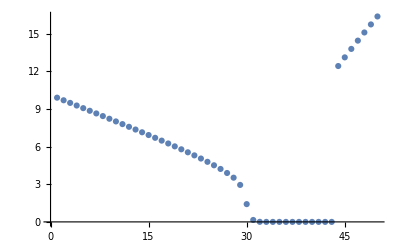

```mathematica
ListPlot[specP1[[1,3;;-1;;2]]-specP1[[1,2;;-2;;2]]]
```

```mathematica
ListPlot[specP1[[1,3;;-1;;2]]-specP1[[1,2;;-2;;2]]]
```

-Graphics-

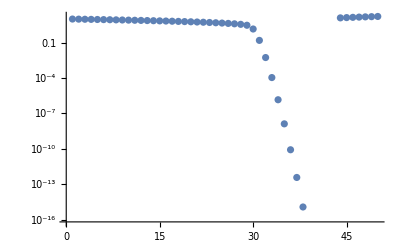

```mathematica
ListLogPlot[specP1[[1,3;;-1;;2]]-specP1[[1,2;;-2;;2]]]
```

```mathematica
Monitor[TCG=Table[Table[Table[ClebschGordan[{j1,m1},{j2,m},{J,M}],{M,-J,J,2}],{m,-j2,j2}],{m1,-j1,j1}];,{M,m,m1}]
```

```mathematica
ListLogPlot[specP1[[1,3;;-1;;2]]-specP1[[1,2;;-2;;2]],PlotRange->All]
```

-Graphics-

```mathematica
Length[vecP]
```

101

```mathematica
j1=50;j2=J-j1;
```

```mathematica
Monitor[TCG=Table[Table[Table[ClebschGordan[{j1,m1},{j2,m},{J,M}],{M,-J,J,2}],{m,-j2,j2}],{m1,-j1,j1}];,{M,m,m1}]
```

ClebschGordan::phy: ThreeJSymbol[{50,-50},{50,-50},{100,98}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{50,-50},{50,-50},{100,96}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{50,-50},{50,-50},{100,94}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

```mathematica
ϵ=10^-9;
enli2={};
enlosT={};
Monitor[Do[enlo={};Do[
fa=Quiet[Table[Table[vecPP[[ke,k]].TCG[[k1,k2]],{k2,1,2j2+1}],{k1,1,2j1+1}]];
rho1=Table[fa[[k1]].fa[[k2]],{k1,1,2j1+1},{k2,1,2j1+1}];
(*AppendTo[enli2,1-Tr[rho1.rho1]];*)
AppendTo[enlo,-Tr[rho1.MatrixLog[rho1+ϵ IdentityMatrix[2j1+1]]]];,{k,60,88(*Length[vecPP[[1]]]*)}];AppendTo[enlosT,enlo];,{ke,1,1}];,{ke,k}]
```

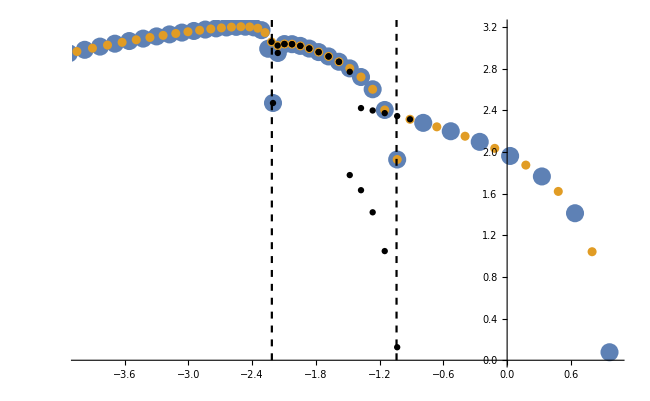

```mathematica
Show[fre,ListPlot[{Transpose[{specP1[[1,60;;88]]/J,enlo}]},PlotStyle->{{Black,PointSize[0.007]}}]]
```

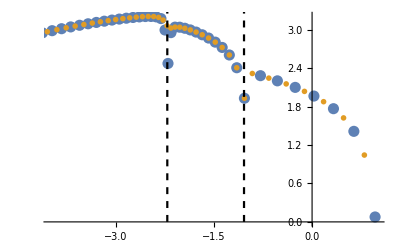
```mathematica
fre=-Graphics-;
```